# Data Science and Machine Learning

## Week 3 exercises

## Entity

Exercise 1: Create an entity of your favourite animal. Display in the same list an image of this animal, its scientific name, family, weight, and length.

```mathematica
Entity["Species","Species:UnciaUncia"]
```

snow leopard

```mathematica
EntityProperties[Entity["Species","Species:UnciaUncia"]]
```

{alternate common names,alternate scientific names,body temperature,class,common name,entity classes,family,genus,image,infraspecies,kingdom,length,maximum recorded lifespan,maximum speed,name,number of child taxa,order,parent taxon,phylum,scientific name,sibling taxa,species,reference,child taxa,taxonomic level,taxonomic sequence,taxonomy graph,weight}

```mathematica
Entity["Species","Species:UnciaUncia"][{ "Image","ScientificName" , "Family", "Weight", "Length"}]
```

{-Graphics-,Uncia uncia,cats,(800.to2800.) oz,98. in}

Exercise 2: 
a) Find the flag of Switzerland.
b) Create one list with the flags of the "BorderingCountries" of Switzerland

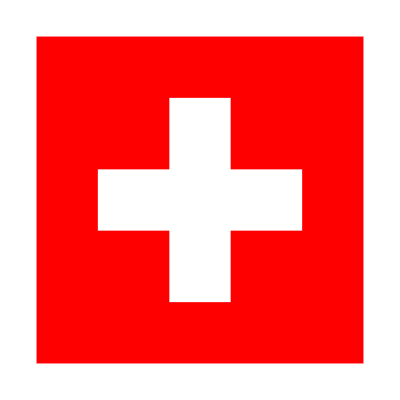

```mathematica
EntityValue[Entity["Country", "Switzerland"], "Flag"]
```

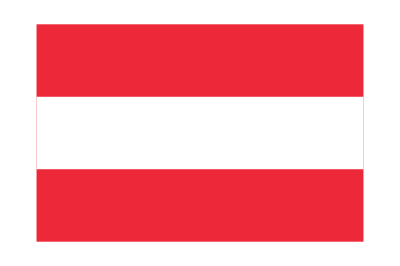


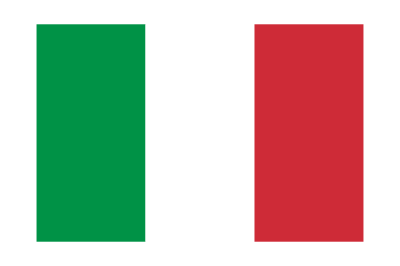
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
EntityValue[Entity["Country","Switzerland"]["BorderingCountries"],"Flag"]
```

Exercise 3: Compute the elevation of Mount Everest divided by the height of the Empire State Building.

```mathematica
Entity["Mountain","MountEverest"]["Elevation"]/Entity["Building","EmpireStateBuilding::h583b"]["Height"]
```

23.2254

Exercise 4: 
a) Create a list of the Population of European Countries
b) Create a Bar Chart using the list you just created. You can try to change the ChartStyle and add some ChartLabels.
c) Create an association of the Population of European Countries using the property "EntityAssociation" 
d) Sort the European countries population from largest to smallest using your association

```mathematica
popEU = EntityValue[EntityClass["Country", "Europe"], "Population"]
```

{2877800 people,77265 people,9006400 people,9449321 people,11589616 people,3280815 people,6948445 people,4105268 people,1207361 people,10708982 people,5792203 people,1326539 people,48865 people,5540718 people,65273512 people,83783945 people,33691 people,10423056 people,65605 people,9660350 people,341250 people,4937796 people,85032 people,60461828 people,95732 people,1859203 people,1886202 people,38137 people,2722291 people,625976 people,2083380 people,441539 people,4033963 people,39244 people,628062 people,17134873 people,5421242 people,37846605 people,10196707 people,19237682 people,33938 people,8790574 people,5459643 people,2078932 people,46754783 people,2637 people,10099270 people,8654618 people,43733759 people,67886004 people,809 people}

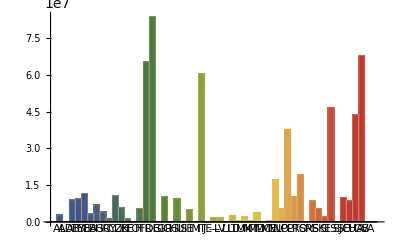

```mathematica
BarChart[popEU,ChartStyle -> "DarkRainbow", ChartLabels ->EntityValue[EntityClass["Country", "Europe"] , "CountryCode"]]
```

```mathematica
popEUasso = EntityValue[EntityClass["Country", "Europe"], "Population", "EntityAssociation"]
```

<|Albania→2877800 people,Andorra→77265 people,Austria→9006400 people,Belarus→9449321 people,Belgium→11589616 people,Bosnia and Herzegovina→3280815 people,Bulgaria→6948445 people,Croatia→4105268 people,Cyprus→1207361 people,Czech Republic→10708982 people,Denmark→5792203 people,Estonia→1326539 people,Faroe Islands→48865 people,Finland→5540718 people,France→65273512 people,Germany→83783945 people,Gibraltar→33691 people,Greece→10423056 people,Guernsey→65605 people,Hungary→9660350 people,Iceland→341250 people,Ireland→4937796 people,Isle of Man→85032 people,Italy→60461828 people,Jersey→95732 people,Kosovo→1859203 people,Latvia→1886202 people,Liechtenstein→38137 people,Lithuania→2722291 people,Luxembourg→625976 people,North Macedonia→2083380 people,Malta→441539 people,Moldova→4033963 people,Monaco→39244 people,Montenegro→628062 people,Netherlands→17134873 people,Norway→5421242 people,Poland→37846605 people,Portugal→10196707 people,Romania→19237682 people,San Marino→33938 people,Serbia→8790574 people,Slovakia→5459643 people,Slovenia→2078932 people,Spain→46754783 people,Svalbard→2637 people,Sweden→10099270 people,Switzerland→8654618 people,Ukraine→43733759 people,United Kingdom→67886004 people,Vatican City→809 people|>

```mathematica
ReverseSort @ popEUasso
```

<|Germany→83783945 people,United Kingdom→67886004 people,France→65273512 people,Italy→60461828 people,Spain→46754783 people,Ukraine→43733759 people,Poland→37846605 people,Romania→19237682 people,Netherlands→17134873 people,Belgium→11589616 people,Czech Republic→10708982 people,Greece→10423056 people,Portugal→10196707 people,Sweden→10099270 people,Hungary→9660350 people,Belarus→9449321 people,Austria→9006400 people,Serbia→8790574 people,Switzerland→8654618 people,Bulgaria→6948445 people,Denmark→5792203 people,Finland→5540718 people,Slovakia→5459643 people,Norway→5421242 people,Ireland→4937796 people,Croatia→4105268 people,Moldova→4033963 people,Bosnia and Herzegovina→3280815 people,Albania→2877800 people,Lithuania→2722291 people,North Macedonia→2083380 people,Slovenia→2078932 people,Latvia→1886202 people,Kosovo→1859203 people,Estonia→1326539 people,Cyprus→1207361 people,Montenegro→628062 people,Luxembourg→625976 people,Malta→441539 people,Iceland→341250 people,Jersey→95732 people,Isle of Man→85032 people,Andorra→77265 people,Guernsey→65605 people,Faroe Islands→48865 people,Monaco→39244 people,Liechtenstein→38137 people,San Marino→33938 people,Gibraltar→33691 people,Svalbard→2637 people,Vatican City→809 people|>

Exercise 5: Plot the population density (Population divided by Land Area) over time between 1950 and 2020 in five countries of your choice. Add a legend and a label

```mathematica
popDensity[country_] := #2[#1,{{"GDP"},{1950,2019}}]/#2[#1,"LandArea"] &[country,CountryData, {1950,2019}];
```

```mathematica
DateListPlot[{popDensity[#1],popDensity[#2], popDensity[#3], popDensity[#4], popDensity[#5]}, PlotLegends ->{#1,#2, #3, #4, #5}, PlotLabel -> "Evolution of population density"] &[Entity["Country","Switzerland"], Entity["Country","France"], Entity["Country","Germany"], Entity["Country","Italy"],Entity["Country","Spain"]]
```

-Graphics-

Exercise 6: Create a GeoRegionValuePlot of the Gini Index in the continent of your choice

```mathematica
GeoRegionValuePlot[LinguisticAssistant->"GiniIndex"]
```

-Graphics-

## Wolfram Data Repository

Exercise 7: Import the "Snowfall Frequency by WMO Station" repository

```mathematica
ResourceObject["Snowfall Frequency by WMO Station"]
snowfall = ResourceData["Snowfall Frequency by WMO Station"]
```

ResourceObject[…]

Exercise 8:  Select the WMO Stations in Japan

```mathematica
snowfallJapan = snowfall[Select[#Country ===Entity["Country","Japan"]&]]
```

-Graphics-

Exercise 9  : Display on a GeoListPlot the WMO Stations in Japan

```mathematica
GeoListPlot[snowfallJapan[All,"Coordinates"], GeoRange -> Entity["Country", "Japan"]]
```

-Graphics-

Exercise 10  : Plot snow frequency from January to December for WMO stations in Japan

```mathematica
DateListPlot[snowfallJapan[ All, {6 ;; 17}]]
```

-Graphics-

## Dataset

Exercise 11 : Here is a dataset based on a class. 
a) Compute the average age of the class, 
b) Compute the share of engineers vs economists. 
c) Create a PieChart of the result, add a legend and change the option plot theme.
Hint: You could Count the numbers of engineers/economists

```mathematica
ds =  Dataset[ <|"Charles" ->  <|"Age" -> 25, "Field" -> "Engineering", "Gender" ->"Male"|> ,
                                      "Sophia" ->  <|"Age" -> 22, "Field" -> "Economics", "Gender" ->"Female" |> ,
               "John" ->  <|"Age" -> 23, "Field" -> "Economics", "Gender" ->"Male" |> ,
               "Maria" ->  <|"Age" -> 24, "Field" -> "Engineering", "Gender" ->"Female" |> ,
               "Karim" ->  <|"Age" -> 22, "Field" -> "Economics", "Gender" ->"Male" |> ,
               "Katharina" ->  <|"Age" -> 26, "Field" -> "Economics", "Gender" ->"Female" |> ,
               "Noémie" ->  <|"Age" -> 22, "Field" -> "Economics", "Gender" ->"Female" |> ,
               "Claudia" ->  <|"Age" -> 21, "Field" -> "Economics", "Gender" ->"Female" |> ,
               "Lionel" ->  <|"Age" -> 24, "Field" -> "Engineering", "Gender" ->"Male" |> ,
               "Andreas" ->  <|"Age" -> 25, "Field" -> "Economics", "Gender" ->"Male" |> ,
               "Martina" ->  <|"Age" -> 22, "Field" -> "Economics", "Gender" ->"Female" |> 
                                      |>]
```

```mathematica
N @ ds[Mean,"Age"]
```

23.2727

```mathematica
numberStudents = Length[ds]
```

11

```mathematica
shareEco=Count[ds[All,"Field"], "Economics"] / numberStudents
shareIng = Count[ds[All,"Field"], "Engineering"] / numberStudents
```

8/11

3/11

```mathematica
PieChart[{shareEco,shareIng}, ChartLegends ->{"Economist", "Engineers"}, PlotTheme -> "Business"]
```

-Graphics-

## Application: carbon intensity of GDP

Exercise 12 : Plot the evolution of GHG emissions per GDP unit for the country of your choice. How do you interpret the result?  
a) Import the CSV file "GHG_EU_csv" and select the country of your choice and years after 1990
b) Convert your dataset into a timeseries using the functions Normal and Timeseries
c) Import GDP data from 1990 to 2019 using CountryData
d) Compute the GHG emissions per GDP unit
e) Plot the result and add a label

```mathematica
ghg = Import["MGT-492/data/GHG_EU.csv", "Dataset", "HeaderLines" -> 1];
ghgCH = ghg[Select[#Country == "Switzerland" &], 7;;];
```

```mathematica
ghgCHconverted =Normal[ghgCH]*1000 //TimeSeries; (*Multiply by 1000 since GHG emissions in thousand tonnes equivalent CO2 *)
```

```mathematica
gdpCH = CountryData["Switzerland",{"GDP", {1990,2019}}];
```

```mathematica
ghgCHperGDP = ghgCHconverted/gdpCH
```

TimeSeries[…]

```mathematica
DateListPlot[ghgCHperGDP,  PlotLabel -> "Carbon intensity of GDP in CH"]
```

-Graphics-

The Carbon intensity of GDP is decreasing. Why so?

```mathematica
DateListPlot[gdpCH,  PlotLabel -> "Evolution of GDP in CH"]
DateListPlot[ghgCH,  PlotLabel -> "Evolution of GHG in CH"]
```

-Graphics-

-Graphics-